### load spike data and network topology

```mathematica
basedir = "/Users/olav/Desktop/Doktorarbeit/Simulationen/NEST/calciumbursts2/";
SetDirectory@basedir;
```

#### import from old MX files

```mathematica
pos=<<"pos.mx";
connections=<<(basedir<>"input/cons.mx");
pars=<<(basedir<>"input/pars.mx")

(* calculate adjacency matrix *)
adjA=Table[0.0,{size/.pars},{size/.pars}];
For[ii=1,ii≤cons/.pars,ii++,
adjA⟦connections⟦ii,1⟧,connections⟦ii,2⟧⟧=1.0
];
adjA2=MatrixPower[adjA,2];

(* calculate degrees *)
degreein=Table[Total@adjA⟦All,ii⟧,{ii,size/.pars}];
degreeout=Table[Total@adjA⟦ii,All⟧,{ii,size/.pars}];
degreeboth=Diagonal@MatrixPower[adjA,2];
degreetotal=degreein+degreeout;
```

{size→100,cons→1200,mindist→0.01,cstrmin→0.1,cstrmax→0.1,thresh→1,topology→new,stepsize→0.5,leaktime→20,syndelay→0,transmittertime→100,transmitterred→0.3,allowbidircons→True,globalstimulation→False,globalconnectivity→False,nondirectionalcons→False,watchitmaxdur→110,analysislength→150,notes→watchit-Topologien fuer die NEST-Simulationen (Vergleich mit Demians TE-Auswertung),compiletime→15:03:36 on Aug 26 2009}

#### import from YAML file

```mathematica
ImportNetworkFromYAML[filename_]:=Module[{instream,cfrom,j,ctolist,adjA,pos,pars},
(* make sure converter and input file exist *)
(* If[!FileExistsQ["/Users/olav/Desktop/Doktorarbeit/Simulationen/networktest4/20090924/C1_05"],Abort[]]; *)
If[!FileExistsQ[filename],Abort[]];
(* load yaml file in raw form *)
instream=First@RunThrough["/Users/olav/Desktop/Doktorarbeit/Simulationen/yaml2mx "<>filename,""];
Print[pars=Sort@DeleteCases[instream,nodes->_]];

adjA=SparseArray[{},{size/.pars,size/.pars},0];
pos=Table[{0,0},{size/.pars}];
instream=nodes/.instream;
For[cfrom=1,cfrom≤Length@instream,cfrom++,
(* pos⟦cfrom⟧=pos/. *)
(* for now, assume all nodes are present here and that they are presented in order *)
If[(id/.instream)≠cfrom,Abort[]];
ctolist=connectedTo/.instream⟦cfrom⟧;
For[j=1,j≤Length@ctolist,j++,adjA⟦cfrom,ctolist⟦j⟧⟧=1];
];
{adjA,pos,pars}
];
{adjA,pos,pars}=ImportNetworkFromYAML["topology-Random.yml"];
```

{cons→1200,createdAt→Mon 5 Apr 2010 20:42:20,minDist→0.01,notes→random topology, for comparison with the Leogang topology,size→100}

```mathematica
(* extract connections list from SparseArray adjacency matrix *)
GetConnections[adjA_]:=Drop[ArrayRules@adjA,-1]⟦All,1⟧;
adjAconnections=Evaluate@GetConnections[adjA];
```

### load and evaluate reconstruction

#### load single reconstruction results

```mathematica
basedir = "/Users/olav/Desktop/Doktorarbeit/Causality/transferentropy-sim/HeavierExternal/te";
SetDirectory@basedir;
```

```mathematica
SetDirectory@basedir;
adjAtest=<<"../../../Causality/granger/output/grangercausality_Leogang1.mx";
```

```mathematica
SetDirectory@basedir;
adjAtest2=<<"../../../Causality/granger/output/grangercausality_Leogang2.mx";
```

```mathematica
adjAtestGC=adjAtest2;
```

```mathematica
adjAtest=<<"adjA_iteration5.mx";
```

```mathematica
SetDirectory@basedir;
xfilename="granger/grangercausality_os_15bins.mx";
adjAtestGC=<<(xfilename);
```

```mathematica
adjAtest2=<<"granger/grangercausality_os_15bins.mx";
```

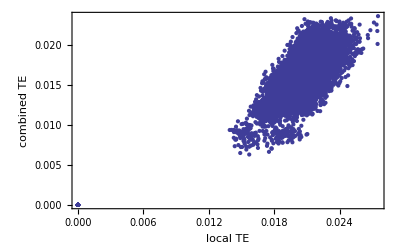

```mathematica
Clear[ii,jj];ListPlot[Flatten[Table[{adjAtest⟦ii,jj⟧,adjAtest2⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"local TE","combined TE"},PlotRange->Automatic]
```

```mathematica
SetDirectory@basedir;globaltransferentropy=<<"/Users/olav/Desktop/Doktorarbeit/Imaging/transferentropy/output/transferentropy_global.mx";
```

```mathematica
SetDirectory@basedir;maximatransferentropy=<<"/Users/olav/Desktop/Doktorarbeit/Imaging/transferentropy/output/transferentropy_maxima.mx";
```

```mathematica
Clear[ii,jj];
ListPlot[Flatten[Table[{adjAtransferentropy⟦ii,jj⟧,adjAtest⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"fitted weight","variance reduction (0,0)"}]
ListPlot[Flatten[Table[{adjAtransferentropy⟦ii,jj⟧,adjAtest2⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"fitted weight","variance reduction (1,1)"}]
ListPlot[Flatten[Table[{adjAtest2⟦ii,jj⟧,adjAtest3⟦ii,jj⟧},{ii,size/.pars},{jj,size/.pars}],1],FrameLabel->{"variance reduction (0,0)","variance reduction (1,1)"}]
```

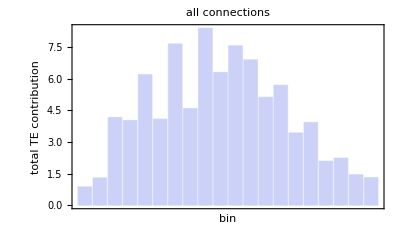

```mathematica
BarChart[Table[Total@Flatten@adjAtest⟦All,All,kk⟧,{kk,1,20}],Frame->True,FrameLabel->{"bin","total TE contribution"},PlotLabel->"all connections"]
```

```mathematica
TElinked=TEnotlinked=TElinkedUnidir=TElinkedBidir=Table[0,{20}];
For[source=1,source≤size/.pars,source++,
For[target=1,target≤size/.pars,target++,
If[MemberQ[GetConnections@adjA,{source,target}],
TElinked+=adjAtest⟦source,target⟧;
If[MemberQ[GetConnections@adjA,{target,source}],
TElinkedBidir+=adjAtest⟦source,target⟧;
,
TElinkedUnidir+=adjAtest⟦source,target⟧;
];
,
TEnotlinked+=adjAtest⟦source,target⟧;
];
];
];
Clear[source,target];
```

```mathematica
BarChart[Table[Total@Flatten@adjAtest⟦All,All,kk⟧,{kk,1,20}],FrameLabel->{"bin","total TE contribution"},PlotLabel->"all connections"]
BarChart[TElinked,Frame->True,FrameLabel->{"bin","total TE contribution"},PlotLabel->"linked"]
BarChart[TEnotlinked,Frame->True,FrameLabel->{"bin","total TE contribution"},PlotLabel->"not linked"]
BarChart[TElinkedUnidir,Frame->True,FrameLabel->{"bin","total TE contribution"},PlotLabel->"linked (uni-directional)"]
BarChart[TElinkedBidir,Frame->True,FrameLabel->{"bin","total TE contribution"},PlotLabel->"linked (bi-directional)"]
```

#### compare adjacency matrix directly

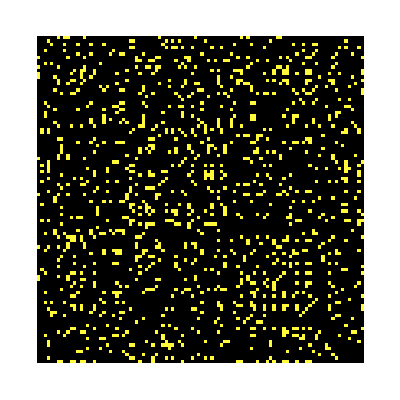

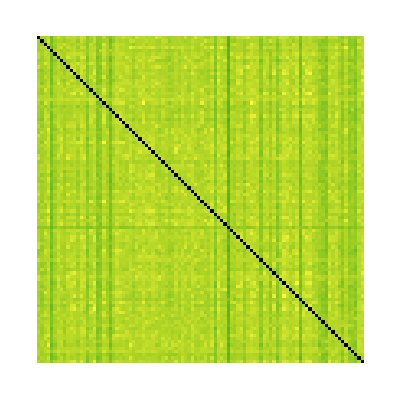

```mathematica
ArrayPlot[adjA,ColorFunction->"AvocadoColors"]
ArrayPlot[adjAtest2,ColorFunction->"AvocadoColors"]
(* ArrayPlot[maximatransferentropy,ColorFunction->"AvocadoColors"] *)
```

{m→-0.0043892,b→0.0148422}

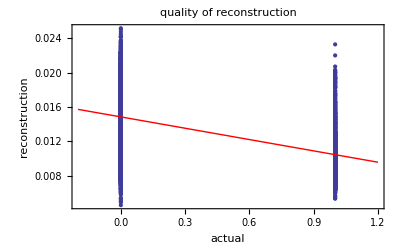

-0.419316

```mathematica
(* compare single entries, 1st order *)
xdata=Drop[Sort@Flatten[Table[{adjA⟦ii,jj⟧,adjAtest⟦ii,jj⟧},{ii,Length@adjA},{jj,Length@adjA}],1],Length@adjA];
xfit=FindFit[xdata,m x+b,{m,b},x]
xplot={ListPlot[xdata,PlotRange->All],Plot[(m x+b)/.xfit,{x,-0.2,1.2},PlotStyle->Red]};
Show[xplot,FrameLabel->{"actual","reconstruction"},PlotLabel->"quality of reconstruction"]
Correlation[xdata⟦All,1⟧,xdata⟦All,2⟧]
Clear[ii,jj,m,x,b,xfit,xplot];
```

```mathematica
SetupCorAdjA:=Module[{xx,ii,jj},
xAdjAcor=Table[0,{size*(size-1)/.pars}];
xx=0;
For[ii=1,ii≤size/.pars,ii++,
For[jj=1,jj≤size/.pars,jj++,
If[ii≠jj,xAdjAcor⟦++xx⟧=adjA⟦ii,jj⟧];
];
]];
```

```mathematica
FindCorAdjA[adjAtest_]:=Module[{ii,jj,xx=0,xcorResult},
xcorResult=Table[0,{size*(size-1)/.pars}];
For[ii=1,ii≤size/.pars,ii++,
For[jj=1,jj≤size/.pars,jj++,
If[ii≠jj,xcorResult⟦++xx⟧=adjAtest⟦ii,jj⟧];
];
];

Correlation[xAdjAcor,xcorResult]
];
```

```mathematica
basedir = "/Users/olav/Desktop/Doktorarbeit/Causality/transferentropy-sim/NoiseFPSnew";
```

```mathematica
SetDirectory@basedir;
tauFs={0,0,0,0,350001,291667,250001,218751,194445,175001,159091,145834,134616,125001,116667,109376,102942,97223,92106,87501,83334,79546,76087,72917,70001,67308,64815,62501,60345,58334};
qualityA=Table[0,{11},{11}];
For[i=0,i≤110,i++,
xtemp=<<("adjA_iteration"<>ToString@i<>".mx");
xpars=<<("pars_iteration"<>ToString@i<>".mx");
(* Print[ToString@Round@(noise/.xpars)/0.03<>" und "<>ToString[(First@First@Position[tauFs,samples/.xpars]-5)/2]]; *)
qualityA⟦1+Round@((noise/.xpars)/0.03),1+(First@First@Position[tauFs,samples/.xpars]-5)/2⟧=FindCorAdjA[xtemp];
];
```

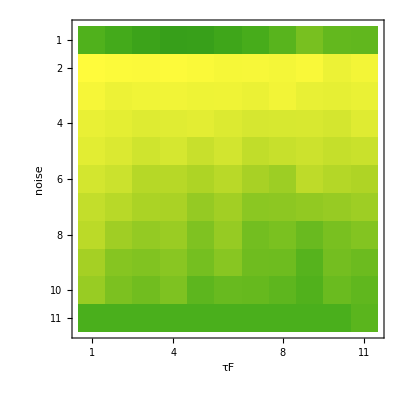

```mathematica
MatrixPlot[qualityA,ColorFunction->"AvocadoColors",FrameLabel->{"noise","τF"}]
```

#### generate ROC curves (old functions)

```mathematica
GenerateROC[xadjA_]:=GenerateROC[xadjA,100];
GenerateROC[xadjA_,xsteps_]:=Module[{xdata,xx,t,xmin,xmax,xstepsize,xP,xTP,xN,xFP,xROCpoints},
xROCpoints=Table[{0,0},{xsteps+1}];
(* compare single entries, 1st order *)
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
(* test if exactly the diagonal elements have been deleted *)
If[Length@xdata!=Length@adjA*(Length[adjA]-1),Print["Warning: length="<>ToString@Length@xdata];];

xmin=Min@Last@Transpose@xdata;
xmax=Max@Last@Transpose@xdata;
xstepsize=(xmax-xmin)/xsteps;
If[xstepsize<10^-9,Abort[]];
(* go through all possible threshold values and compute the ROC data points *)
For[t=0,t≤xsteps,t++,
xx=xmin+t*xstepsize;
(*ShowStatus["xx="<>ToString@xx];*)
xP=Length@Cases[xdata,{1,_}];
xTP=Length@Cases[xdata,{1,_?((#>xx)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>xx)&)}];
xROCpoints⟦t+1⟧=N@{xFP/xN,xTP/xP};
];

xROCpoints
];
```

```mathematica
GenerateROCfn[xdata_,fraction_]:=Module[{xx,xP,xTP,xN,xFP,xROCpointsLocal,middle},
(* go through all possible threshold values and compute the ROC data points *)
xx=Min@Flatten@xdata+(Max@Flatten@xdata-Min@Flatten@xdata)*fraction;
xP=Length@Cases[xdata,{1,_}];
xTP=Length@Cases[xdata,{1,_?((#>xx)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>xx)&)}];
N@{xFP/xN,xTP/xP}
];
x2Data[xadjA_]:=Module[{ii,jj,xdata},
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
(* test if exactly the diagonal elements have been deleted *)
If[Length@xdata!=Length@adjA*(Length[adjA]-1),Print["Warning: length="<>ToString@Length@xdata]];
xdata
];
```

```mathematica
SetDirectory@basedir;
xROClist={};
For[i=0,i≤3,i++,
xtemp=<<("adjA_iteration"<>ToString[i]<>".mx");
(*xpars=<<("pars_iteration"<>ToString@i<>".mx");*)
ShowStatus["i = "<>ToString[i]<>"..."];
AppendTo[xROClist,GenerateROC@xtemp];
];
(*Print[Length@xROClist];*)
ShowStatus["done."];
Clear[i,xtemp,xpars];
```

#### generate ROC curves (adaptive functions)

```mathematica
GenerateROCsmart[xadjA_]:=Module[{xdata,xmin,xmax,xROCpoints,oldRL},
xROCpoints={{0,0},{1,1}};
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
(* test if exactly the diagonal elements have been deleted *)
If[Length@xdata!=Length@adjA*(Length[adjA]-1),Print["Warning: length="<>ToString@Length@xdata];];

xmin=N@Min@Last@Transpose@xdata;
xmax=N@Max@Last@Transpose@xdata;
If[xmax-xmin<10^-9,Abort[]];
oldRL=$RecursionLimit;
$RecursionLimit=1000;
xROCpoints=GenerateROCrecursive[xdata,{0,0},xmax,{1,1},xmin,xROCpoints,0.04];
$RecursionLimit=oldRL;
Sort@xROCpoints
];
GenerateROCrecursive[xdata_,left_,xmax_,right_,xmin_,xROCpoints_,minDist2D_]:=Module[{xx,xP,xTP,xN,xFP,xROCpointsLocal,middle},
xROCpointsLocal=xROCpoints;
(* go through all possible threshold values and compute the ROC data points *)
xx=N@((xmin+xmax)/2);
xP=Length@Cases[xdata,{1,_}];
xTP=Length@Cases[xdata,{1,_?((#>xx)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>xx)&)}];
middle=N@{xFP/xN,xTP/xP};
AppendTo[xROCpointsLocal,middle];
(* Print["New ROC point: "<>ToString@middle<>", xx="<>ToString@InputForm@xx<>", left="<>ToString@left<>", xmin="<>ToString@InputForm@xmin<>", right="<>ToString@right<>", xmax="<>ToString@InputForm@xmax];
Pause[0.1]; *)
If[Length@Cases[xdata,{_,_?((#>xmin)&&(#<xmax)&)}]>1,
If[Norm[middle-left]>minDist2D,
xROCpointsLocal=GenerateROCrecursive[xdata,left,xmax,middle,xx,xROCpointsLocal,minDist2D]];
If[Norm[right-middle]>minDist2D,
xROCpointsLocal=GenerateROCrecursive[xdata,middle,xx,right,xmin,xROCpointsLocal,minDist2D]];
];
xROCpointsLocal
];
```

```mathematica
basedir = "/Users/olav/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/SeparatedTest";
SetDirectory@basedir;
```

```mathematica
basedir = "/Users/olav/Desktop/Doktorarbeit/Causality/transferentropy-sim/Paris/LeogangTopology";
SetDirectory@basedir;
```

```mathematica
importlist=(<<("adjA_iteration"<>ToString@#<>".mx")&/@Range[0,0]);
```

```mathematica
importlist=<<"adjA_iteration0.mx";
importlist2=Table[Transpose[importlist⟦All,All,ii⟧],{ii,Last@Dimensions@importlist}];
```

```mathematica
adjAtest=First@importlist2;
```

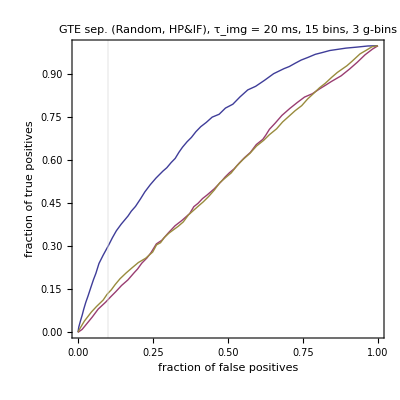

```mathematica
ListPlot[GenerateROCsmart/@importlist2,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"GTE sep. (Random, HP&IF), τ_img = 20 ms, 15 bins, 3 g-bins",PlotRange->All]
```

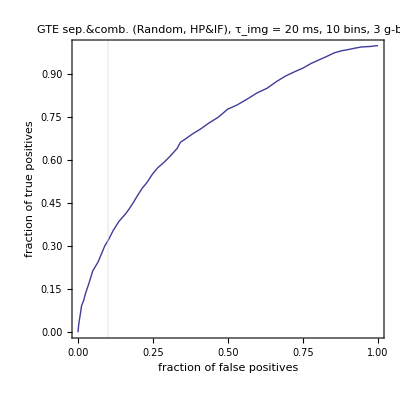

```mathematica
ListPlot[GenerateROCsmart@Total[importlist2⟦1;;2⟧],Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"GTE sep.&comb. (Random, HP&IF), τ_img = 20 ms, 10 bins, 3 g-bins",PlotRange->All]
```

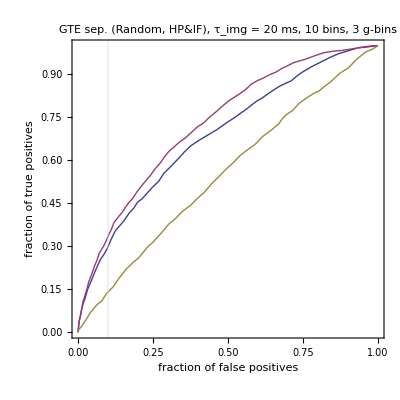

```mathematica
ListPlot[GenerateROCsmart/@importlist2,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"GTE sep. (Random, HP&IF), τ_img = 20 ms, 10 bins, 3 g-bins",PlotRange->All]
```

```mathematica
Print[<<"pars_iteration0.mx"];
```

{executable→teglobalsim,iteration→1,size→100,rawdatabins→255,bins→15,cutoff→-1,globalbins→3,samples→359951,p→1,noise→-1,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/RandomTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/SeparatedTest/adjA_iteration0.mx}

#### improve reconstruction using DPI

```mathematica
adjAtest=<<"adjA_iteration0.mx";
Print[<<"pars_iteration0.mx"];
(* normalization *)
adjAtest-=Min@adjAtest;
adjAtest/=Max@adjAtest;
```

{executable→teglobalsim,iteration→1,size→100,rawdatabins→255,bins→5,cutoff→-1,globalbins→3,samples→359951,p→1,noise→0,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/RandomTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/RandomTopology/adjA_iteration0.mx}

```mathematica
adjAtest2=adjAtest;
```

```mathematica
adjAtestList={adjAtest2};
```

```mathematica
cutcount=0;
threshold=0.05;
trials=0;
While[cutcount<6*size*size/.pars,
trials++;
(* For[trials=1,trials≤10000,trials++, *)
nodeA=Random[Integer,{1,size/.pars}];
nodeB=Random[Integer,{1,size/.pars}];
nodeC=Random[Integer,{1,size/.pars}];
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
If[(adjAtest2⟦nodeA,nodeB⟧>adjAtest2⟦nodeA,nodeC⟧+threshold)&&(adjAtest2⟦nodeB,nodeC⟧>adjAtest2⟦nodeA,nodeC⟧+threshold),
adjAtest2⟦nodeA,nodeC⟧*=0.2;
cutcount++];
];
If[Mod[trials,1111]==0, ShowStatus["iteration: "<>ToString@trials<>", "<>ToString@cutcount<>" links 'deleted'."]];
];
ShowStatus[ToString@cutcount<>" links deleted. done."];
Clear[nodeA,nodeB,nodeC,cutcount,threshold,trials];
AppendTo[adjAtestList,adjAtest2];
```

```mathematica
Histogram@Flatten@adjAtest
```

```mathematica
Histogram@Flatten@adjAtest2
```

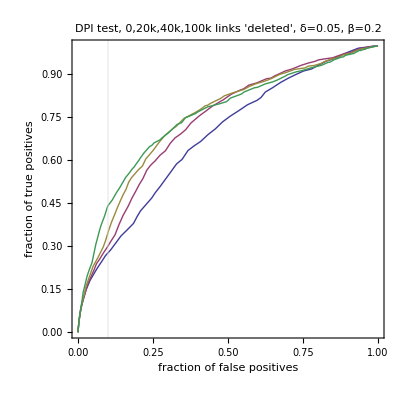

```mathematica
ListPlot[GenerateROCsmart/@adjAtestList,Joined->True,GridLines->{{0.1},{}},Axes->False,AspectRatio->1,FrameLabel->{"fraction of false positives","fraction of true positives"},PlotLabel->"DPI test, 0,20k,40k,100k links 'deleted', δ=0.05, β=0.2",PlotRange->All]
```

```mathematica
Print[<<"pars_iteration0.mx"];
```

{executable→teglobalsim,iteration→1,size→100,rawdatabins→255,bins→5,cutoff→-1,globalbins→3,samples→359951,p→1,noise→0,tauF→20,OverrideRescalingQ→0,HighPassFilterQ→1,InstantFeedbackTermQ→1,inputfile→../../Simulationen/NEST/calciumbursts2/Paris/RandomTopology/noisefree_rawCalcium_uchar_20ms.dat,outputfile→Paris/RandomTopology/adjA_iteration0.mx}

```mathematica
xROC3D=Flatten[Table[{i+1,xROClist⟦i,x,1⟧,xROClist⟦i,x,2⟧},{i,Length@xROClist},{x,101}],1];
```

```mathematica
ListPlot3D[xROC3D,AspectRatio->1,ColorFunction->"AvocadoColors",ImageSize->Medium]
```

```mathematica
xdata=DeleteCases[Sort@Flatten[Table[{adjA⟦ii,jj⟧,adjAtest⟦ii,jj⟧},{ii,Length@adjA},{jj,Length@adjA}],1],{0,0.0}];
(* test if exactly the diagonal elements have been deleted *)
If[Length@xdata!=Length@adjA*(Length[adjA]-1),Print@Length@xdata;Abort[]];
xhistodata={Last@Transpose@Cases[xdata,{0,_}],Last@Transpose@Cases[xdata,{1,_}]};Histogram[xhistodata,ImageSize->Large]
```

```mathematica
tenpercent={};
For[i=1,i≤33,i++,
index=1;
While[xROClist⟦i,index,1⟧>0.2,index++];
AppendTo[tenpercent,{1+i,xROClist⟦i,index,2⟧}]
];
```

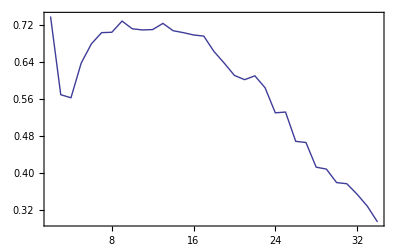

```mathematica
ListPlot[tenpercent,Joined->True]
```

#### improve reconstruction using DPI - the ARACHNE two thresholds way

```mathematica
adjAtest-=Min@adjAtest;
adjAtest/=Max@adjAtest;
```

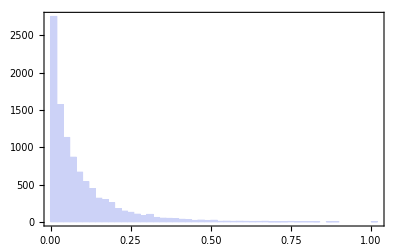

```mathematica
Histogram@Flatten@adjAtest
```

```mathematica
ImbalanceIndex[AB_,ACx_,BC_]:=Min[1,(2 ACx)/(AB+BC)];
imbalanceArray=Table[0,{size/.pars},{size/.pars},{size/.pars}];
(* go through the triples exaustively, and save imbalace index *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
ShowStatus["running: nodeA = "<>ToString@nodeA];
For[nodeB=1,nodeB≤size/.pars,nodeB++,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
imbalanceArray⟦nodeA,nodeB,nodeC⟧=ImbalanceIndex[adjAtest⟦nodeA,nodeB⟧,adjAtest⟦nodeA,nodeC⟧,adjAtest⟦nodeB,nodeC⟧]
];
]]];
Clear[nodeA,nodeB,nodeC];
ShowStatus["done."];
```

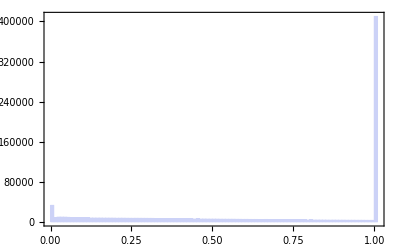

```mathematica
Histogram@Flatten@imbalanceArray
```

```mathematica
imbalanceArray⟦1,20,32⟧
```

0.673163

```mathematica
Single2DROCpoint[xadjA_,tPresent_,tImbalanced_]:=Module[{ii,jj,nodeA,nodeB,nodeC,modifiedA,xdata,xP,xTP,xN,xFP,β=0.5,xmaxi},
modifiedA=xadjA;
(* go through the triples exaustively *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
(* ShowStatus["running: nodeA = "<>ToString@nodeA]; *)
For[nodeB=1,nodeB≤size/.pars,nodeB++,
If[(xadjA⟦nodeA,nodeB⟧>tPresent)||(xadjA⟦nodeB,nodeA⟧>tPresent),
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine AC *)
If[(xadjA⟦nodeA,nodeB⟧>tPresent)&&(xadjA⟦nodeA,nodeC⟧>tPresent)&&(xadjA⟦nodeB,nodeC⟧>tPresent),
If[imbalanceArray⟦nodeA,nodeB,nodeC⟧<tImbalanced,modifiedA⟦nodeA,nodeC⟧=β*modifiedA⟦nodeA,nodeC⟧]
];
(* examine CA *)
If[(xadjA⟦nodeC,nodeB⟧>tPresent)&&(xadjA⟦nodeB,nodeA⟧>tPresent)&&(xadjA⟦nodeC,nodeA⟧>tPresent),
If[imbalanceArray⟦nodeC,nodeB,nodeA⟧<tImbalanced,modifiedA⟦nodeC,nodeA⟧=β*modifiedA⟦nodeC,nodeA⟧]
];
]];
]]];

xdata=DeleteCases[Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,modifiedA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
xP=Length@Cases[xdata,{1,_}];
xmaxi=Max@Flatten@modifiedA;
xTP=Length@Cases[xdata,{1,_?((#>tPresent*xmaxi)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>tPresent*xmaxi)&)}];
N@{xFP/xN,xTP/xP}
]
```

```mathematica
x3Ddata=Table[{"leer"},{21},{21}];
For[tPresent=0,tPresent≤20,tPresent++,
For[tImbalanced=0,tImbalanced≤20,tImbalanced++,
tP=tPresent/20.;
tI=tImbalanced/20.;
ShowStatus["running: tPresent = "<>ToString@tP<>", tImbalanced = "<>ToString@tI<>" ..."];
x3Ddata⟦tPresent+1,tImbalanced+1⟧=Flatten@{tI,Single2DROCpoint[adjAtest,tP,tI]};
]];
Clear[tp,tI,tPresent,tImbalanced];
x3Ddata=DeleteCases[Flatten[x3Ddata,1],{"leer"}];
ShowStatus["done"];
```

```mathematica
Single2DROCpoint[adjAtest,0.5,0.5]
```

{0.00149425,0.0766667}

```mathematica
ListPlot3D[x3Ddata]
```

-Graphics3D-

```mathematica
x3Ddata
```

```mathematica
xtest={1,2,3};
{a,#}&/@xtest
```

{{a,1},{a,2},{a,3}}

```mathematica
size/.pars
```

100

```mathematica
ImbalanceIndex[AB_,ACx_,BC_]:=Min[1,(2 ACx)/(AB+BC)];
GenerateImbalanceArray[xadjA_]:=Module[{nodeA,nodeB,nodeC,imbalanceArray},
imbalanceArray=Table[0,{size/.pars},{size/.pars},{size/.pars}];
(* go through the triples exaustively, and save imbalace index *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
ShowStatus["generating imbalanceArray: nodeA = "<>ToString@nodeA];
For[nodeB=1,nodeB≤size/.pars,nodeB++,
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
imbalanceArray⟦nodeA,nodeB,nodeC⟧=ImbalanceIndex[xadjA⟦nodeA,nodeB⟧,xadjA⟦nodeA,nodeC⟧,xadjA⟦nodeB,nodeC⟧]
];
]]];
Return@imbalanceArray
];

Generate2DROCsmart[xadjA_]:=Generate2DROCsmart[xadjA,0.04];
Generate2DROCsmart[xadjA_,maxdist_]:=Module[{ii,steps,data3D={},imbalanceArray={}},
imbalanceArray=GenerateImbalanceArray[xadjA];
steps=Ceiling[1/maxdist];
For[ii=0,ii<steps,ii++,
AppendTo[data3D,{ii/steps,#}&/@Generate2DROCsmartInner[xadjA,imbalanceArray,ii/steps,maxdist]];
];
ShowStatus["done."];
Return[Flatten/@data3D]
];

Generate2DROCsmartInner[xadjA_,imbalanceArray_,tImbalanced_,maxdist_]:=Module[{xdata,xmin,xmax,xROCpoints,oldRL},
xROCpoints={{0,0},{1,1}};
xdata=DeleteCases[Sort@Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,xadjA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
(* test if exactly the diagonal elements have been deleted *)
If[Length@xdata!=Length@adjA*(Length[adjA]-1),Print["Warning: length="<>ToString@Length@xdata];];

xmin=N@Min@Last@Transpose@xdata;
xmax=N@Max@Last@Transpose@xdata;
If[xmax-xmin<10^-9,Abort[]];
oldRL=$RecursionLimit;
$RecursionLimit=1000;
xROCpoints=Generate2DROCrecursive[xadjA,imbalanceArray,{0,0},xmax,{1,1},xmin,xROCpoints,maxdist,tImbalanced];
$RecursionLimit=oldRL;
Return@Sort@xROCpoints
];

Generate2DROCrecursive[xadjA_,imbalanceArray_,left_,xmax_,right_,xmin_,xROCpoints_,maxDist2D_,tImbalanced_]:=Module[{tPresent,xP,xTP,xN,xFP,xROCpointsLocal,middle,nodeA,nodeB,nodeC,modifiedA,β=0.8,xdata,xmaxi},
xROCpointsLocal=xROCpoints;
(* go through all possible threshold values and compute the ROC data points *)
tPresent=N@((xmin+xmax)/2);
ShowStatus["Generate2DROCrecursive: tPresent = "<>ToString@N@tPresent<>", tImbalanced = "<>ToString@N@tImbalanced<>" ..."];
modifiedA=xadjA;
(* go through the triples exaustively *)
For[nodeA=1,nodeA≤size/.pars,nodeA++,
(* ShowStatus["running: nodeA = "<>ToString@nodeA]; *)
For[nodeB=1,nodeB≤size/.pars,nodeB++,
If[(xadjA⟦nodeA,nodeB⟧>tPresent)||(xadjA⟦nodeB,nodeA⟧>tPresent),
For[nodeC=1,nodeC≤size/.pars,nodeC++,
(* if the nodes are really a triple *)
If[(nodeA≠nodeB)&&(nodeA≠nodeC)&&(nodeB≠nodeC),
(* examine AC *)
If[(xadjA⟦nodeA,nodeB⟧>tPresent)&&(xadjA⟦nodeA,nodeC⟧>tPresent)&&(xadjA⟦nodeB,nodeC⟧>tPresent),
If[imbalanceArray⟦nodeA,nodeB,nodeC⟧<tImbalanced,modifiedA⟦nodeA,nodeC⟧=β*modifiedA⟦nodeA,nodeC⟧]
];
(* examine CA *)
If[(xadjA⟦nodeC,nodeB⟧>tPresent)&&(xadjA⟦nodeB,nodeA⟧>tPresent)&&(xadjA⟦nodeC,nodeA⟧>tPresent),
If[imbalanceArray⟦nodeC,nodeB,nodeA⟧<tImbalanced,modifiedA⟦nodeC,nodeA⟧=β*modifiedA⟦nodeC,nodeA⟧]
];
]];
]]];

xdata=DeleteCases[Flatten[Table[If[ii≠jj,{adjA⟦ii,jj⟧,modifiedA⟦ii,jj⟧},{"nix"}],{ii,Length@adjA},{jj,Length@adjA}],1],{"nix"}];
xP=Length@Cases[xdata,{1,_}];
xmaxi=Max@Flatten@modifiedA;
xTP=Length@Cases[xdata,{1,_?((#>tPresent)&)}];
xN=Length@Cases[xdata,{0,_}];
xFP=Length@Cases[xdata,{0,_?((#>tPresent)&)}];
middle=N@{xFP/xN,xTP/xP};
AppendTo[xROCpointsLocal,middle];

If[Length@Cases[xdata,{_,_?((#>xmin)&&(#<xmax)&)}]>1,
If[Norm[middle-left]>maxDist2D,
xROCpointsLocal=Generate2DROCrecursive[xadjA,imbalanceArray,left,xmax,middle,tPresent,xROCpointsLocal,maxDist2D,tImbalanced]];
If[Norm[right-middle]>maxDist2D,
xROCpointsLocal=Generate2DROCrecursive[xadjA,imbalanceArray,middle,tPresent,right,xmin,xROCpointsLocal,maxDist2D,tImbalanced]];
];
Return@xROCpointsLocal
];
```

```mathematica
x3Ddata=Generate2DROCsmart[adjAtest,0.35];
```

#### MiniTopologyTests - style examinantion

```mathematica
basedir = "/Users/olav/Desktop/Doktorarbeit/Causality/transferentropy-sim/MiniTopologyTests";
experiment="b";
```

```mathematica
SetDirectory@basedir;
xCORlist={};
SetupCorAdjA;
For[i=0,i≤15,i++,
xtemp=<<("adjA_iteration"<>ToString@i<>"_"<>experiment<>".mx");
xpars=<<("pars_iteration"<>ToString@i<>"_"<>experiment<>".mx");
ShowStatus["i = "<>ToString[i]<>"..."];
AppendTo[xCORlist,{tauF/.xpars,bins/.xpars,FindCorAdjA@xtemp}];
];
(*Print[Length@xCORlist];*)
ShowStatus["done."];
Clear[i,xtemp,xpars];
```

```mathematica
xCORlist
```

{{2,3,Correlation[{1,1},{4.×10^-6,8.×10^-6}]},{2,6,Correlation[{1,1},{0.000046,0.000032}]},{2,9,Correlation[{1,1},{0.0001,0.000088}]},{2,12,Correlation[{1,1},{0.00022,0.000207}]},{4,3,Correlation[{1,1},{9.×10^-6,0.000015}]},{4,6,Correlation[{1,1},{0.00009,0.00006}]},{4,9,Correlation[{1,1},{0.000207,0.000178}]},{4,12,Correlation[{1,1},{0.00044,0.000403}]},{6,3,Correlation[{1,1},{0.000015,0.000021}]},{6,6,Correlation[{1,1},{0.000143,0.000094}]},{6,9,Correlation[{1,1},{0.000304,0.000255}]},{6,12,Correlation[{1,1},{0.000653,0.000601}]},{8,3,Correlation[{1,1},{0.000017,0.000029}]},{8,6,Correlation[{1,1},{0.00018,0.000125}]},{8,9,Correlation[{1,1},{0.000418,0.000361}]},{8,12,Correlation[{1,1},{0.000877,0.000827}]}}

```mathematica
ListPlot3D[xCORlist,PlotLabel->experiment]
```

```mathematica
Histogram3D[xdata,(*{Automatic,{0.002}},*)PlotRange->All,ImageSize->Large(*,PlotLabel->xfilename*)]
```

-Graphics3D-

#### combine several reconstructions

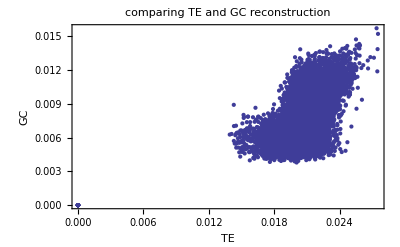

```mathematica
(* combine TE and GC results *)
ListPlot[Transpose@{Flatten@adjAtest,Flatten@adjAtest2},PlotRange->Automatic,Frame->True,Axes->False,FrameLabel->{"TE","GC"},PlotLabel->"comparing TE and GC reconstruction"]

(* xdata=adjAtransferentropy/(Mean@adjAtransferentropy)+xresult/(Mean@xresult);
xdata=Drop[Sort@Flatten[Table[{adjA⟦ii,jj⟧,xdata⟦ii,jj⟧},{ii,Length@xdata},{jj,Length@xdata}],1],Length@xdata]; *)
```

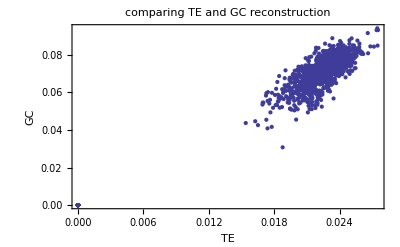

```mathematica
(* compare TE and GC results *)
ListPlot[Transpose@{Flatten@(adjAtransferentropy*adjA),Flatten@(xresult*adjA)},PlotRange->Automatic,Frame->True,Axes->False,FrameLabel->{"TE","GC"},PlotLabel->"comparing TE and GC reconstruction for present connections"]
```

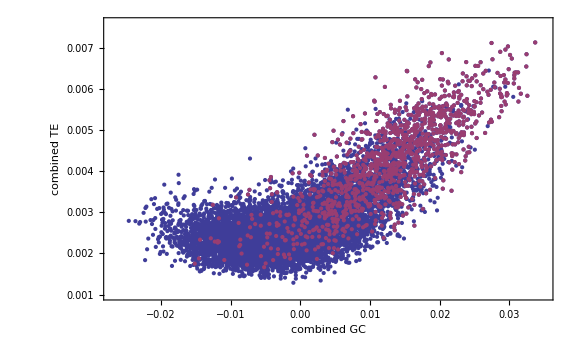

```mathematica
(* compare TE and GC results *)
ListPlot[{Transpose@{Flatten@adjAtestGC,Flatten@adjAtestTE},Transpose@{Flatten@(adjAtestGC*adjA),Flatten@(adjAtestTE*adjA)}},PlotRange->{{-0.027,0.035},{0.001,0.0076}},FrameLabel->{"combined GC","combined TE"},ImageSize->Large,PlotStyle->PointSize[Medium]]
```

#### extend to global TE

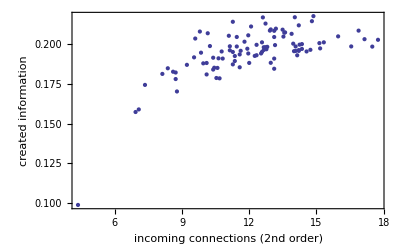

```mathematica
ListPlot[Table[{Sqrt@N@Total@adjA2⟦ii⟧,globaltransferentropy⟦ii,2⟧},{ii,Length@globaltransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections (2nd order)","recieved information from global"}]
```

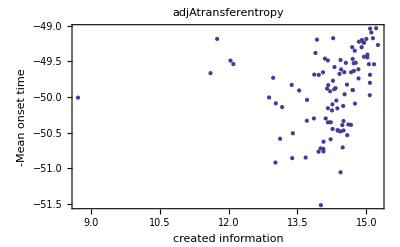

Correlation: 0.211251

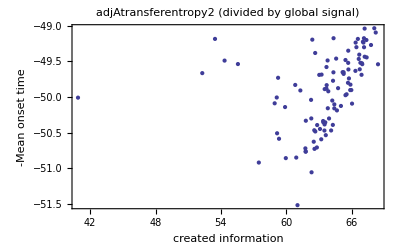

Correlation: 0.338019

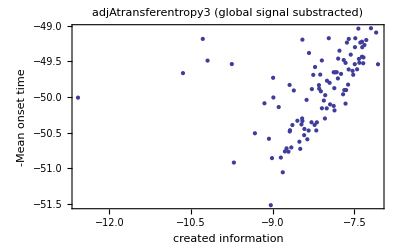

Correlation: 0.432565

```mathematica
adjAtransferentropy2=Table[adjAtransferentropy⟦ii,jj⟧/(globaltransferentropy⟦ii,1⟧+globaltransferentropy⟦jj,2⟧),{ii,100},{jj,100}];
adjAtransferentropy3=Table[adjAtransferentropy⟦ii,jj⟧-(globaltransferentropy⟦ii,1⟧+globaltransferentropy⟦jj,2⟧),{ii,100},{jj,100}];
ListPlot[{Table[{Total@adjAtransferentropy⟦ii⟧,-Mean@Drop[xtimes⟦ii,All,2⟧,1]},{ii,100}]},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"created information","-Mean onset time"},PlotLabel->"adjAtransferentropy"]
Print["Correlation: "<>ToString@Correlation[Table[Total@adjAtransferentropy⟦ii⟧,{ii,100}],Table[-Mean@Drop[xtimes⟦ii,All,2⟧,1],{ii,100}]]];

ListPlot[{Table[{Total@adjAtransferentropy2⟦ii⟧,-Mean@Drop[xtimes⟦ii,All,2⟧,1]},{ii,100}]},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"created information","-Mean onset time"},PlotLabel->"adjAtransferentropy2 (divided by global signal)"]
Print["Correlation: "<>ToString@Correlation[Table[Total@adjAtransferentropy2⟦ii⟧,{ii,100}],Table[-Mean@Drop[xtimes⟦ii,All,2⟧,1],{ii,100}]]];

ListPlot[{Table[{Total@adjAtransferentropy3⟦ii⟧,-Mean@Drop[xtimes⟦ii,All,2⟧,1]},{ii,100}]},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"created information","-Mean onset time"},PlotLabel->"adjAtransferentropy3 (global signal substracted)"]
Print["Correlation: "<>ToString@Correlation[Table[Total@adjAtransferentropy3⟦ii⟧,{ii,100}],Table[-Mean@Drop[xtimes⟦ii,All,2⟧,1],{ii,100}]]];
```

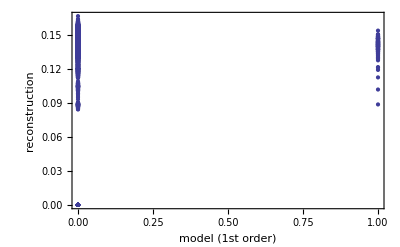

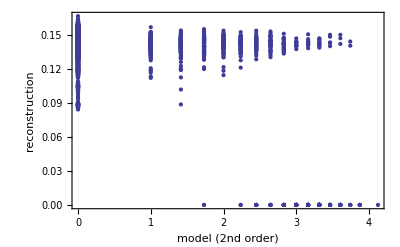

```mathematica
ListPlot[Flatten[Table[{adjA⟦ii,jj⟧,adjAtransferentropy⟦ii,jj⟧},{ii,Length@adjAtransferentropy},{jj,Length@adjAtransferentropy}],1],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"model (1st order)","reconstruction"}]
ListPlot[Flatten[Table[{Sqrt@adjA2⟦ii,jj⟧,adjAtransferentropy⟦ii,jj⟧},{ii,Length@adjAtransferentropy},{jj,Length@adjAtransferentropy}],1],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"model (2nd order)","reconstruction"}]
```

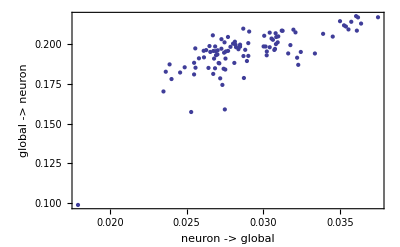

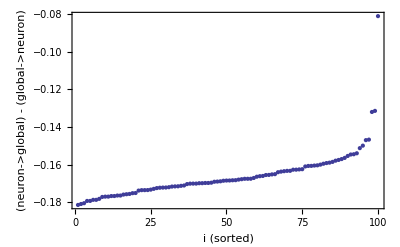

```mathematica
ListPlot[globaltransferentropy,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"neuron -> global","global -> neuron"}]
ListPlot[Sort[First@#-Second@#&/@globaltransferentropy],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"i (sorted)","(neuron->global) - (global->neuron)"}]
```

14.3058

14.4373

0.0302156

0.158886

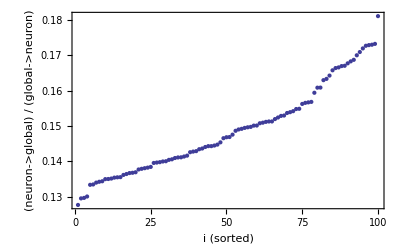

```mathematica
ii=2;
Total@adjAtransferentropy⟦ii,All⟧
Total@adjAtransferentropy⟦All,ii⟧
globaltransferentropy⟦ii,1⟧
globaltransferentropy⟦1,ii⟧

ListPlot[Sort[(First@#)/(Second@#)&/@globaltransferentropy],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"i (sorted)","(neuron->global) / (global->neuron)"}]
```

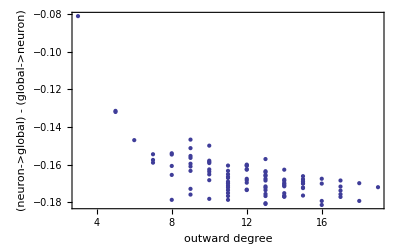

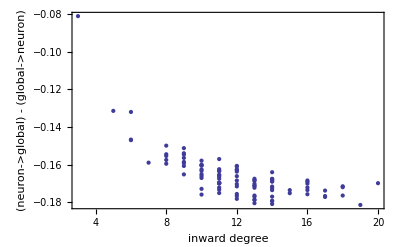

```mathematica
ListPlot[Table[{Total@adjA⟦ii⟧,globaltransferentropy⟦ii,1⟧-globaltransferentropy⟦ii,2⟧},{ii,Length@globaltransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outward degree","(neuron->global) - (global->neuron)"}]
ListPlot[Table[{Total@adjA⟦All,ii⟧,globaltransferentropy⟦ii,1⟧-globaltransferentropy⟦ii,2⟧},{ii,Length@globaltransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"inward degree","(neuron->global) - (global->neuron)"}]
```

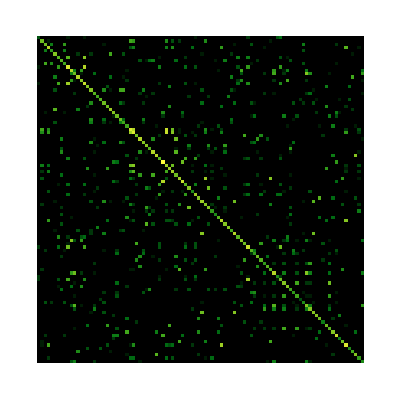

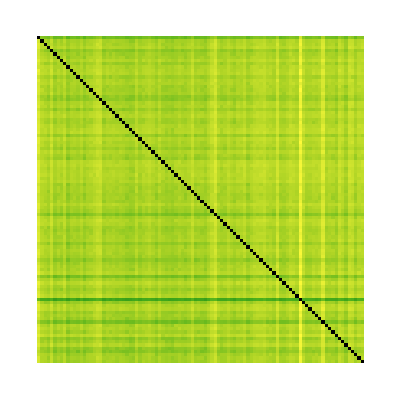

```mathematica
adjAtransferentropy2=Table[adjAtransferentropy⟦ii,jj⟧/(globaltransferentropy⟦ii,1⟧+globaltransferentropy⟦jj,2⟧),{ii,100},{jj,100}];
ArrayPlot[adjA2⟦1;;Length@adjAtransferentropy,1;;Length@adjAtransferentropy⟧,ColorFunction->"AvocadoColors"]
ArrayPlot[adjAtransferentropy2,ColorFunction->"AvocadoColors"]
```

#### examine maxima TE

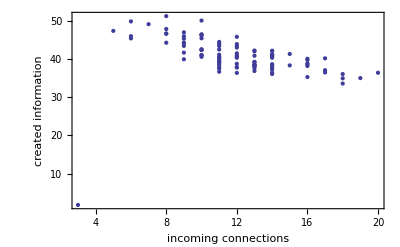

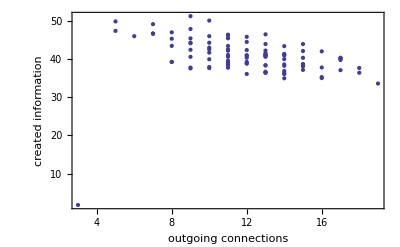

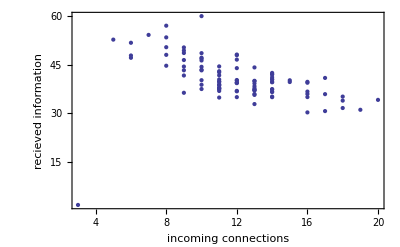

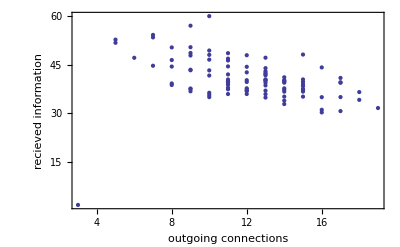

```mathematica
ListPlot[Table[{Total@adjA⟦All,ii⟧,Total@maximatransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections","created information"}]
ListPlot[Table[{Total@adjA⟦ii⟧,Total@maximatransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections","created information"}]

ListPlot[Table[{Total@adjA⟦All,ii⟧,Total@maximatransferentropy⟦All,ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections","recieved information"}]
ListPlot[Table[{Total@adjA⟦ii⟧,Total@maximatransferentropy⟦All,ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections","recieved information"}]
```

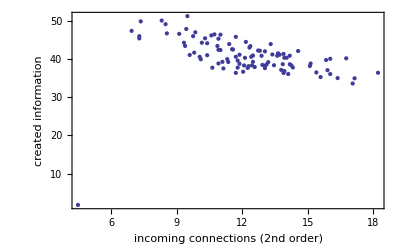

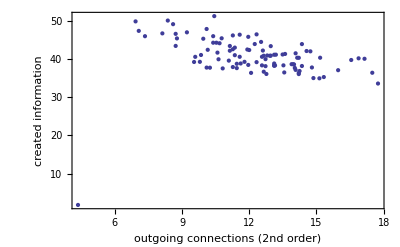

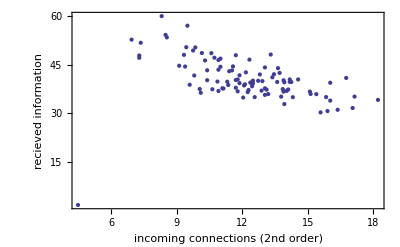

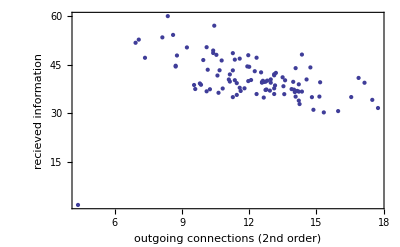

```mathematica
ListPlot[Table[{Sqrt@N@Total@adjA2⟦All,ii⟧,Total@maximatransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections (2nd order)","created information"}]
ListPlot[Table[{Sqrt@N@Total@adjA2⟦ii⟧,Total@maximatransferentropy⟦ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections (2nd order)","created information"}]

ListPlot[Table[{Sqrt@N@Total@adjA2⟦All,ii⟧,Total@maximatransferentropy⟦All,ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"incoming connections (2nd order)","recieved information"}]
ListPlot[Table[{Sqrt@N@Total@adjA2⟦ii⟧,Total@maximatransferentropy⟦All,ii⟧},{ii,Length@adjAtransferentropy}],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"outgoing connections (2nd order)","recieved information"}]
```

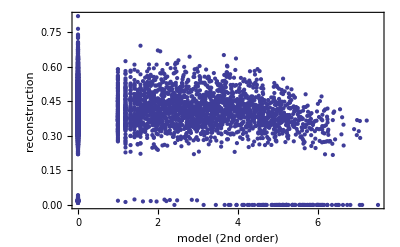

```mathematica
adjAx=N@(MatrixPower[adjA,4]^(1/4));
ListPlot[Flatten[Table[{adjAx⟦ii,jj⟧,maximatransferentropy⟦ii,jj⟧},{ii,Length@maximatransferentropy},{jj,Length@maximatransferentropy}],1],PlotRange->All,Frame->True,Axes->False,FrameLabel->{"model (2nd order)","reconstruction"}]
```

#### examine iterated TE

```mathematica
basedir = "/Users/olav/Desktop/Doktorarbeit/Causality/transferentropy-sim/iterated_test";
SetDirectory@basedir;
```

```mathematica
xtemp=<<"adjA_iteration0.mx";
```

```mathematica
xExistList=Last@Transpose@Cases[GetConnections@adjA,{1,_}]
```

{7,9,10,15,38,49,63,65,74,75}

```mathematica
%-1
```

{6,8,9,14,37,48,62,64,73,74}

```mathematica
xNonExistList=Complement[Range[2,100],xExistList]
```

{2,3,4,5,6,8,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,39,40,41,42,43,44,45,46,47,48,50,51,52,53,54,55,56,57,58,59,60,61,62,64,66,67,68,69,70,71,72,73,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

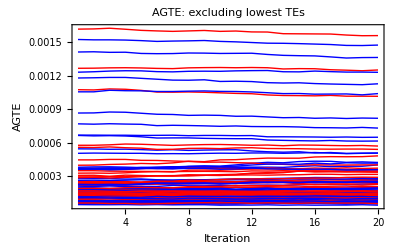

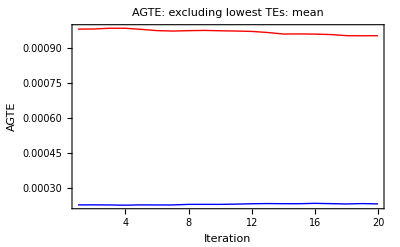

```mathematica
endindex=20;
ListPlot[Flatten[{xtemp⟦xExistList,1;;endindex⟧,xtemp⟦xNonExistList,1;;endindex⟧},1],Joined->True,PlotStyle->{Red,Blue},FrameLabel->{"Iteration","AGTE"},PlotRange->All,PlotLabel->"AGTE: excluding lowest TEs"]
ListPlot[{Mean@xtemp⟦xExistList,1;;endindex⟧,Mean@xtemp⟦xNonExistList,1;;endindex⟧},Joined->True,PlotStyle->{Red,Blue},FrameLabel->{"Iteration","AGTE"},PlotRange->All,PlotLabel->"AGTE: excluding lowest TEs: mean"]
```